# Expanded Computational Geometry Graph

WWW Graph of Computational Geometry for Link Analysis Ranking Experiments

### DetailsDetailsGive a detailed description of the data, including information about the size, structure, and history of the content elements. This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the data was first created or how and why it is used within a given field. Include all relevant background or contextual information related to the data, its development, and its usage.

WWW Graph of Computational Geometry for Link Analysis Ranking Experiments: The Base Set is constructed by including all out-links of each page in the Root Set. We use the refined algorithm for detecting intra-domain links.

## Data DefinitionsData DefinitionsDefine the content of the resource by assigning values to ResourceData. The icon inside ResourceData below represents the ResourceObject defined within this notebook. Evaluating the ResourceData[]=xxxx cell below defines the default content element of this resource, which will be returned by ResourceData[obj]. Evaluating the subsequent cells defines additional content elements with the specified element names. The element name is used to access the associated content via ResourceData[obj,element]. The default content element is assigned a name either based on the Head of the data or set to "Content". Define as many elements as needed using different element names. You can insert the icon using the "Insert ResourceObject" button in the "Tools" above. Elements set to CloudObject, File, or LocalObject values will be interpreted as the content of those locations. Each content element must have a string name, preferably camel case. (Typical names describe the content element, and include "Dataset", "Text" and "TimeSeries"). Elements defined as functions are automatically applied to the other elements of the resource. For example, ResourceData[,"Vertices"]=(VertexList[#Graph]&) will define an element named "Vertices" which is derived from the "Graph" element when requested by the user.

### Primary Content

```mathematica
ResourceData[{{}},"Graph"]=CloudObject["https://www.wolframcloud.com/obj/5b79cacf-b3c3-420b-9927-a7c1541ec26d"];
```

### Additional Data Elements (optional)

```mathematica
ResourceData[{{}},"ByteCount"]=
```

```mathematica
ResourceData[{{}},"Description"]=
```

```mathematica
ResourceData[{{}},"EdgeCount"]=
```

```mathematica
ResourceData[{{}},"EdgeProperty"]=
```

```mathematica
ResourceData[{{}},"FullGraph"]=CloudObject["https://www.wolframcloud.com/obj/851ca076-cfc5-4098-b81e-b1cc9ab42bcf"];
```

```mathematica
ResourceData[{{}},"LongDescription"]=
```

```mathematica
ResourceData[{{}},"Name"]=
```

```mathematica
ResourceData[{{}},"Source"]=
```

```mathematica
ResourceData[{{}},"StandardName"]=
```

```mathematica
ResourceData[{{}},"Summary"]=
```

```mathematica
ResourceData[{{}},"VertexCount"]=
```

```mathematica
ResourceData[{{}},"VertexProperty"]=
```

## ExamplesExamplesDemonstrate the data's usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (using Tools ▶ Insert Delimiter). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic usage "◼ ""Scope: "show the breadth of the data "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the data relates to other data "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Retrieve the graph:

```mathematica
ResourceData[{{}}]
```

-Graphics-

Summary properties:

```mathematica
ResourceData["Expanded Computational Geometry Graph",All]["Summary"]
```

Name | Expanded Computational Geometry Graph
VertexCount | 1226
EdgeCount | 3953
Description | WWW Graph of Computational Geometry for Link Analysis Ranking Experiments
ByteCount | 1075.69 kB

### Basic Applications

Show the power-law degree distribution of the graph:

```mathematica
g=ResourceData[{{}}];
```

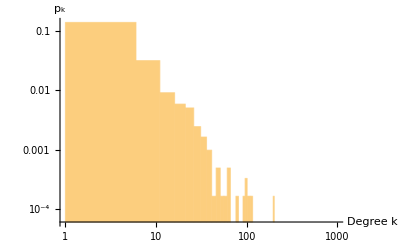

```mathematica
Histogram[VertexDegree[g],{"Log",{1,1000,5}},{"Log","PDF"},]
```

Show a table of properties:

```mathematica
Dataset[Table[<|i->i[g]|>,{i,{GraphReciprocity,GlobalClusteringCoefficient,GraphAssortativity}}]]
```

Dataset[<>]

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this data.

Wolfram

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the data and/or its components.

Datasets for Experiments on Link Analysis Ranking Algorithms, "http://www.cs.toronto.edu/~tsap/experiments/datasets/index.html"

### Detailed Source InformationDetailed Source InformationAdd bibliographic details about the original source and publication of the data.

#### Author/Creator

#### Source Title

#### Source Date

#### Source Publisher

#### Geographic Coverage

#### Temporal Coverage

#### Source Language

#### Rights

### LinksLinksList additional URLs or hyperlinks for external information related to the data.

### KeywordsKeywordsList relevant terms that should be used to include the data in search results.

WWW Graph

### CategoriesCategoriesSelect any categories which the data covers.

Mathematics

### Content TypesContent TypesSelect any of the types of data included in the content elements.

Graphs

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this data.

### Related SymbolsRelated SymbolsList documented, system-level Wolfram Language symbols related to the data.

## Author NotesAuthor NotesInclude any notes you would like to be published along with the resource. These notes will be available to all users and can include known limitations or possible improvements to the data.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.